```mathematica
Clear[x,y,z,U1,U2,z0,w1x,w2y,w1z,w2z,g, mRb]
U[x_,y_,z_]:=-U1 Exp[-2 x^2/w1x^2-2 z^2/w1z^2]-U2 Exp[-2 y^2/w2y^2-2 z^2/w2z^2]+mRb g z;
ax=SeriesCoefficient[U[x,0,z0],{x,0,2}]
ay=SeriesCoefficient[U[0,y,z0],{y,0,2}]
az=SeriesCoefficient[U[0,0,z],{z,z0,2}]
bz=SeriesCoefficient[U[0,0,z],{z,z0,1}]
```

(2 ⅇ^(-(2 z0^2)/w1z^2) U1)/w1x^2

(2 ⅇ^(-(2 z0^2)/w2z^2) U2)/w2y^2

(2 ⅇ^(-(2 z0^2)/w1z^2) U1)/w1z^2+(2 ⅇ^(-(2 z0^2)/w2z^2) U2)/w2z^2-(8 ⅇ^(-(2 z0^2)/w1z^2) U1 z0^2)/w1z^4-(8 ⅇ^(-(2 z0^2)/w2z^2) U2 z0^2)/w2z^4

g mRb+(4 ⅇ^(-(2 z0^2)/w1z^2) U1 z0)/w1z^2+(4 ⅇ^(-(2 z0^2)/w2z^2) U2 z0)/w2z^2

```mathematica
a=w1x^2/w1z^2+w2y^2/w2z^2;
b=w1x^2/w1z^4+w2y^2/w2z^4;
c=Sqrt[b/(a-1)];
z0=-1/(2 c);
U1=mRb g w1x^2/(2a)c Exp[2 z0^2/w1z^2];
U2=mRb g w2y^2/(2a)c Exp[2 z0^2/w2z^2];
```

-0.0000228783

3.24881×10^-6

3.24881×10^-6

77.0945

77.0945

1.22823×10^-6

{z→-0.0000465228}

56.4198

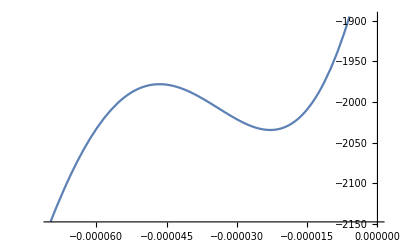

```mathematica
w1x=65 10^-6;
w2y=65 10^-6;
w1z=68 10^-6;
w2z=68 10^-6;

mRb=1.443160648 10^-25;
g=9.81;
hbar=1.054571628 10^-34;
kB = 1.3806504 10^-23;
aB=5.2917720859 10^-11;
as=96 aB;

a=w1x^2/w1z^2+w2y^2/w2z^2;
b=w1x^2/w1z^4+w2y^2/w2z^4;
c=√(b/(a-1));
z0=-1/(2c)//N
U1=mRb g w1x^2/(2a)c Exp[2 z0^2/w1z^2];
U1/kB
U2=mRb g w2y^2/(2a)c Exp[2 z0^2/w2z^2];
U2/kB
ωx=√(2ax/mRb);
ωx/(2π)
ωz=√(2az/mRb);
ωz/(2π)
lx=√(hbar/(mRb ωx))
uz[z_]:=U[0,0,z]/hbar/ωx;
s1=FindRoot[D[uz[z],z]==0,{z,4z0}]
z1=z/.s1;
uz[z1]-uz[z0]
Plot[uz[z],{z,3/2 z1,0}]
```

```mathematica
N0=1.2 10^5;
mu=15^(2/5)/2(N0 as/lx)^(2/5)hbar ωx;
mu/(hbar ωx)
Ri=√(2 mu/(mRb ωx^2))
wxb=ωx/ωx
z0b=z0/lx
z1b=z1/lx
U1/hbar/ωx
geff=g/(lx ωx^2)
√(-geff/z0b/a)
√(-g/z0/a)/(2π)
```

17.6895

7.30554×10^-6

1.

-18.6271

-37.878

878.07

34.0395

1.

77.0945

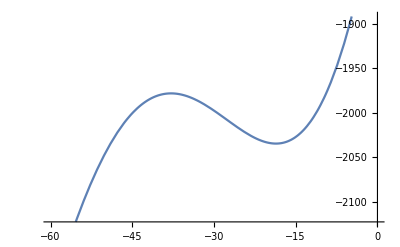

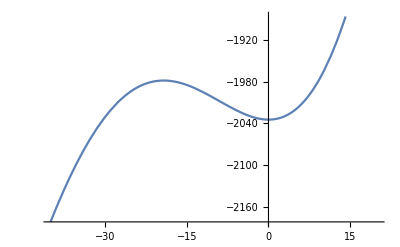

```mathematica
u1z[z_]:=-2 U1/(hbar ωx)  Exp[-2(z)^2 lx^2/w1z^2]+mRb g/(hbar ωx) (z) lx;
Plot[u1z[z],{z,-60,0}]
u3z[z_]:=-2 U1/(hbar ωx)  Exp[-2(z+z0/lx)^2 lx^2/w1z^2]+mRb g/(hbar ωx) (z+z0/lx) lx;
Plot[u3z[z],{z,-40,20}]
```

-Graphics3D-

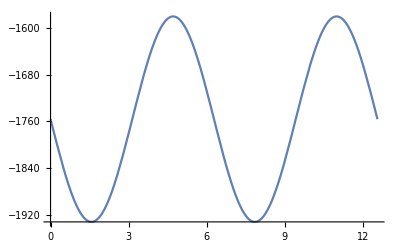

4.71239

1.5708

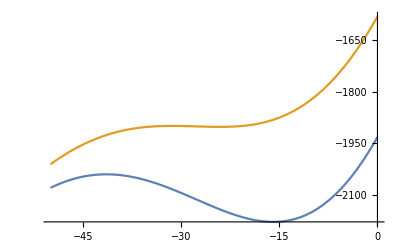

-24.1343

-31.389

2.85288

```mathematica
Ua[t_]:= U1 (1+0.1Sin[ t]);
u2z[z_,t_]:=-2 Ua[t]/(hbar ωx)  Exp[-2z^2 lx^2/w1z^2]+mRb g/(hbar ωx) z lx;
Plot3D[u2z[z,t],{z,-50,0},{t,0,4π}]
Plot[u2z[0,t],{t,0,4π}]
t0=t/.FindRoot[D[u2z[0,t],t]==0,{t,5}]
t1=t/.FindRoot[D[u2z[0,t],t]==0,{t,1}]
Plot[{u2z[z,t1],u2z[z,t0]},{z,-50,0}]

z0p=z/.FindRoot[D[u2z[z,t0],z]==0,{z,z0/lx}]
z1p=z/.FindRoot[D[u2z[z,t0],z]==0,{z,3z0/lx}]
(u2z[z1p,t0]-u2z[z0p,t0])
```

NSolve::ifun: Inverse functions are being used by NSolve, so some solutions may not be found; use Reduce for complete solution information.

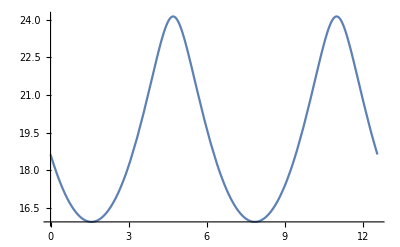

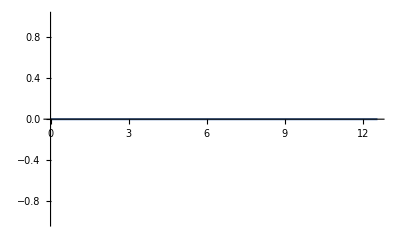

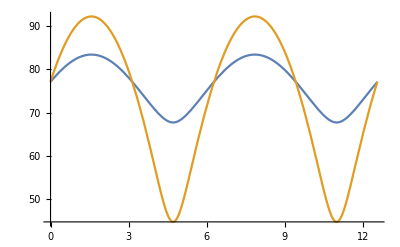

```mathematica
ss=NSolve[mRb g + 8Ua[t] z/w1z^2 Exp[-2 z^2/w1z^2]==0,z];
zt[t_]:=Evaluate[z/.ss[[1]]]
Plot[Re[zt[t]/lx],{t,0,4π},PlotRange->All]
Plot[Im[zt[t]/lx],{t,0,4π},PlotRange->All]
Ux[t_]:=2 Ua[t]/w1x^2 ⅇ^(-(2 zt[t]^2)/w1z^2);
ωxt[t_]:=√(2Ux[t]/mRb);
Uz[t_]:=(4 ⅇ^(-(2 zt[t]^2)/w1z^2) Ua[t])/w1z^2-(16 ⅇ^(-(2 zt[t]^2)/w1z^2) Ua[t] zt[t]^2)/w1z^4;
ωzt[t_]:=√(2Uz[t]/mRb);
Plot[{ωxt[t]/(2π),ωzt[t]/(2π)},{t,0,4π}]
```

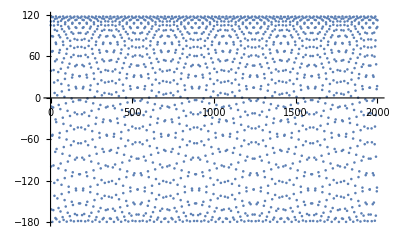

{319}

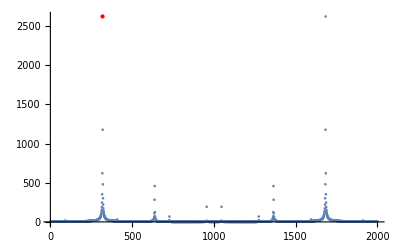

1315

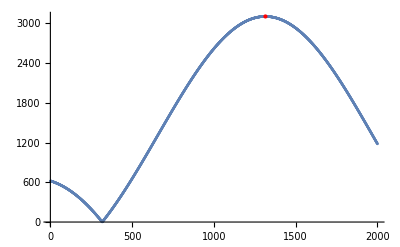

{6.2831}

```mathematica
nt=2000;
tt=Table[n,{n,nt}];
wzt=Evaluate[ωzt[tt]];
ww = wzt -Mean[wzt];
ListPlot[Re[ww]]
f=Abs[Fourier[Re[ww]]];
pos=Position[f,Max[f]][[1]]
Show[ListPlot[f], Graphics[{Red, Point[{pos[[1]], f[[pos[[1]]]]}]}], PlotRange->All]
fr = Abs[Fourier[wzt  Exp[2 Pi I (pos[[1]] - 2) N[Range[0, nt-1 ]]/nt], FourierParameters->{0,2/nt}]];
frpos = Position[fr, Max[fr]][[1,1]]
Show[ListPlot[fr], Graphics[{Red, Point[{frpos, fr[[frpos]]}]}], PlotRange->All]
N[nt/(pos-2+2 (frpos-1)/nt)]
```

```mathematica
udim[x_,y_,z_]:=(2U1)/(hbar ωx)-U1/(hbar ωx)(Exp[(-2x^2 lx^2)/w1x^2]+Exp[(-2y^2 lx^2)/w2y^2])Exp[-(2(z+z0/lx)^2 lx^2)/w2z^2]+mRb g/(hbar ωx) (z+z0/lx) lx;
umin=udim[0,0,0]

ContourPlot3D[udim[x,y,z]-umin==10,{x,-20,20},{y,-20,20},{z,-20,20}]
```

-278.273

-Graphics3D-

```mathematica
Plot3D[Exp[-2x^2]+Exp[-2y^2],{x,-3,3},{y,-3,3}]
Plot3D[Exp[-2x^2-2y^2],{x,-3,3},{y,-3,3},PlotRange->All]
```

-Graphics3D-

-Graphics3D-

```mathematica
t0 =60 10^-3;
dt = 0.002;
ωx t0/dt
```

14532.

```mathematica
2π 340/ωx
```

4.41017

```mathematica
√19//N
```

4.3589

```mathematica
n=2;
l=1;
√(l+3n +2n l +2n^2)
```

√19

{{0,1,√2,√3,2},{√5,2 √2,√11,√14,√17},{√14,√19,2 √6,√29,√34}}

{0,1,√2,√3,2,√5,2 √2,√11,√14,√14,√17,√19,2 √6,√29,√34}

{0.,1.,1.41421,1.73205,2.,2.23607,2.82843,3.31662,3.74166,3.74166,4.12311,4.3589,4.89898,5.38516,5.83095}

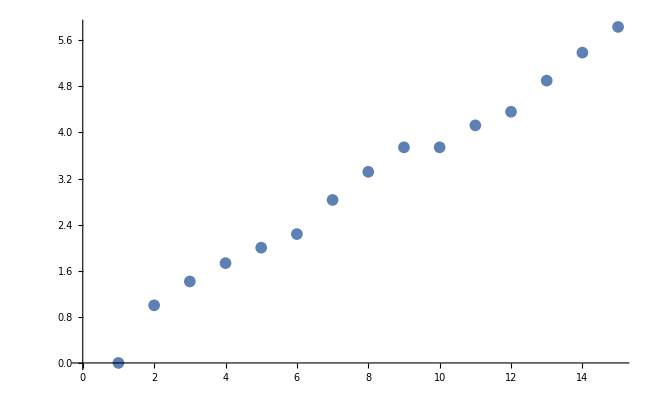

```mathematica
aa=Table[√(l+3n +2n l +2n^2),{n,0,2},{l,0,4}]
bb = Sort[Flatten[aa],#1<#2&]
bb//N
ListPlot[bb]
```

```mathematica
260
```